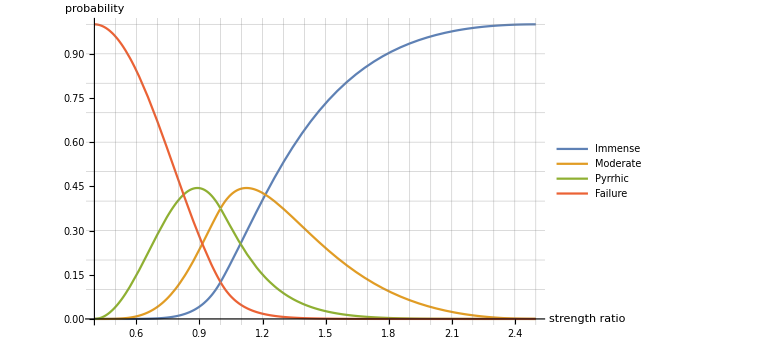

```mathematica
p[r_]:=Piecewise[{
{0,r<0.4},
{25/18 r^2(1-2/5 1/r)^2,0.4≤r&&r<1},
{1-25/(18 r^2)(1-2/5 r)^2,1≤r&&r<2.5},
{1,r>=2.5}
},
2];
pIm[r_]:=p[r]^3;
pMod[r_]:=3 p[r]^2(1-p[r]);
pPyr[r_]:=3(1-p[r])^2 p[r];
pFail[r_]:=(1-p[r])^3;


Plot[{pIm[r],pMod[r],pPyr[r],pFail[r]},{r,0.4,2.5},
PlotLegends->{"Immense","Moderate","Pyrrhic","Failure"},
GridLines->{Range[0.4,2.5,0.1],Range[0,1,0.1]},
ImageSize->Large,
AxesLabel->{"strength ratio","probability"}]
```

```mathematica
table=Table[
Join[{r},Round[{pIm[r],pMod[r],pPyr[r],pFail[r]}*1000]*0.1],{r,0.4,2.5,0.05}
]
```

{{0.4,0.,0.,0.,100.},{0.45,0.,0.,1.,99.},{0.5,0.,0.1,4.1,95.9},{0.55,0.,0.3,8.8,90.9},{0.6,0.,0.9,14.9,84.2},{0.65,0.1,2.1,21.7,76.2},{0.7,0.2,4.1,28.7,67.},{0.75,0.5,7.2,35.2,57.2},{0.8,1.1,11.5,40.3,47.1},{0.85,2.2,17.1,43.6,37.1},{0.9,4.2,23.6,44.4,27.8},{0.95,7.4,30.7,42.4,19.5},{1.,12.5,37.5,37.5,12.5},{1.05,19.1,42.2,31.,7.6},{1.1,26.2,44.2,24.9,4.7},{1.15,33.4,44.2,19.5,2.9},{1.2,40.4,42.8,15.1,1.8},{1.25,47.1,40.3,11.5,1.1},{1.3,53.3,37.3,8.7,0.7},{1.35,59.,34.,6.5,0.4},{1.4,64.2,30.6,4.9,0.3},{1.45,69.,27.3,3.6,0.2},{1.5,73.2,24.1,2.6,0.1},{1.55,77.,21.,1.9,0.1},{1.6,80.4,18.2,1.4,0.},{1.65,83.3,15.7,1.,0.},{1.7,86.,13.3,0.7,0.},{1.75,88.2,11.3,0.5,0.},{1.8,90.3,9.4,0.3,0.},{1.85,92.,7.8,0.2,0.},{1.9,93.5,6.4,0.1,0.},{1.95,94.8,5.1,0.1,0.},{2.,95.9,4.1,0.1,0.},{2.05,96.8,3.1,0.,0.},{2.1,97.6,2.4,0.,0.},{2.15,98.2,1.7,0.,0.},{2.2,98.8,1.2,0.,0.},{2.25,99.2,0.8,0.,0.},{2.3,99.5,0.5,0.,0.},{2.35,99.7,0.3,0.,0.},{2.4,99.9,0.1,0.,0.},{2.45,100.,0.,0.,0.},{2.5,100.,0.,0.,0.}}

```mathematica
Export["C:\\cygwin64\\home\\jmft2\\Documents\\pnw\\pnw-battle-outcomes.txt",
table,"Table","FieldSeparators"->"\t\t"];
```

```mathematica
Grid[{{"r","Immense","Moderate","Pyrrhic","Fail"},{0.4,0.,0.,0.,1.},{0.45,0.,0.,0.01,0.99},{0.5,0.,0.001,0.041,0.9590000000000001},{0.55,0.,0.003,0.088,0.909},{0.6,0.,0.009000000000000001,0.149,0.842},{0.65,0.001,0.021,0.217,0.762},{0.7000000000000001,0.002,0.041,0.28700000000000003,0.67},{0.75,0.005,0.07200000000000001,0.352,0.5720000000000001},{0.8,0.011,0.115,0.403,0.47100000000000003},{0.85,0.022,0.171,0.436,0.371},{0.9,0.042,0.23600000000000002,0.444,0.278},{0.9500000000000001,0.074,0.307,0.424,0.195},{1.,0.125,0.375,0.375,0.125},{1.05,0.191,0.422,0.31,0.076},{1.1,0.262,0.442,0.249,0.047},{1.1500000000000001,0.334,0.442,0.195,0.029},{1.2,0.404,0.428,0.151,0.018000000000000002},{1.25,0.47100000000000003,0.403,0.115,0.011},{1.3,0.533,0.373,0.08700000000000001,0.007},{1.35,0.59,0.34,0.065,0.004},{1.4000000000000001,0.642,0.306,0.049,0.003},{1.45,0.6900000000000001,0.273,0.036000000000000004,0.002},{1.5,0.732,0.241,0.026000000000000002,0.001},{1.55,0.77,0.21,0.019,0.001},{1.6,0.804,0.182,0.014,0.},{1.6500000000000001,0.833,0.157,0.01,0.},{1.7,0.86,0.133,0.007,0.},{1.75,0.882,0.113,0.005,0.},{1.8,0.903,0.094,0.003,0.},{1.85,0.92,0.078,0.002,0.},{1.9000000000000001,0.935,0.064,0.001,0.},{1.95,0.9480000000000001,0.051000000000000004,0.001,0.},{2.,0.9590000000000001,0.041,0.001,0.},{2.05,0.968,0.031,0.,0.},{2.1,0.976,0.024,0.,0.},{2.15,0.982,0.017,0.,0.},{2.2,0.988,0.012,0.,0.},{2.25,0.992,0.008,0.,0.},{2.3000000000000003,0.995,0.005,0.,0.},{2.35,0.997,0.003,0.,0.},{2.4,0.999,0.001,0.,0.},{2.45,1.,0.,0.,0.},{2.5,1.,0.,0.,0.}}]
```

r | Immense | Moderate | Pyrrhic | Fail
0.4 | 0. | 0. | 0. | 1.
0.45 | 0. | 0. | 0.01 | 0.99
0.5 | 0. | 0.001 | 0.041 | 0.959
0.55 | 0. | 0.003 | 0.088 | 0.909
0.6 | 0. | 0.009 | 0.149 | 0.842
0.65 | 0.001 | 0.021 | 0.217 | 0.762
0.7 | 0.002 | 0.041 | 0.287 | 0.67
0.75 | 0.005 | 0.072 | 0.352 | 0.572
0.8 | 0.011 | 0.115 | 0.403 | 0.471
0.85 | 0.022 | 0.171 | 0.436 | 0.371
0.9 | 0.042 | 0.236 | 0.444 | 0.278
0.95 | 0.074 | 0.307 | 0.424 | 0.195
1. | 0.125 | 0.375 | 0.375 | 0.125
1.05 | 0.191 | 0.422 | 0.31 | 0.076
1.1 | 0.262 | 0.442 | 0.249 | 0.047
1.15 | 0.334 | 0.442 | 0.195 | 0.029
1.2 | 0.404 | 0.428 | 0.151 | 0.018
1.25 | 0.471 | 0.403 | 0.115 | 0.011
1.3 | 0.533 | 0.373 | 0.087 | 0.007
1.35 | 0.59 | 0.34 | 0.065 | 0.004
1.4 | 0.642 | 0.306 | 0.049 | 0.003
1.45 | 0.69 | 0.273 | 0.036 | 0.002
1.5 | 0.732 | 0.241 | 0.026 | 0.001
1.55 | 0.77 | 0.21 | 0.019 | 0.001
1.6 | 0.804 | 0.182 | 0.014 | 0.
1.65 | 0.833 | 0.157 | 0.01 | 0.
1.7 | 0.86 | 0.133 | 0.007 | 0.
1.75 | 0.882 | 0.113 | 0.005 | 0.
1.8 | 0.903 | 0.094 | 0.003 | 0.
1.85 | 0.92 | 0.078 | 0.002 | 0.
1.9 | 0.935 | 0.064 | 0.001 | 0.
1.95 | 0.948 | 0.051 | 0.001 | 0.
2. | 0.959 | 0.041 | 0.001 | 0.
2.05 | 0.968 | 0.031 | 0. | 0.
2.1 | 0.976 | 0.024 | 0. | 0.
2.15 | 0.982 | 0.017 | 0. | 0.
2.2 | 0.988 | 0.012 | 0. | 0.
2.25 | 0.992 | 0.008 | 0. | 0.
2.3 | 0.995 | 0.005 | 0. | 0.
2.35 | 0.997 | 0.003 | 0. | 0.
2.4 | 0.999 | 0.001 | 0. | 0.
2.45 | 1. | 0. | 0. | 0.
2.5 | 1. | 0. | 0. | 0.

```mathematica
CsvFirst[%160]
```

{{r,Immense,Moderate,Pyrrhic,Fail},{0.4,0.,0.,0.,1.},{0.45,0.,0.,0.01,0.99},{0.5,0.,0.001,0.041,0.959},{0.55,0.,0.003,0.088,0.909},{0.6,0.,0.009,0.149,0.842},{0.65,0.001,0.021,0.217,0.762},{0.7,0.002,0.041,0.287,0.67},{0.75,0.005,0.072,0.352,0.572},{0.8,0.011,0.115,0.403,0.471},{0.85,0.022,0.171,0.436,0.371},{0.9,0.042,0.236,0.444,0.278},{0.95,0.074,0.307,0.424,0.195},{1.,0.125,0.375,0.375,0.125},{1.05,0.191,0.422,0.31,0.076},{1.1,0.262,0.442,0.249,0.047},{1.15,0.334,0.442,0.195,0.029},{1.2,0.404,0.428,0.151,0.018},{1.25,0.471,0.403,0.115,0.011},{1.3,0.533,0.373,0.087,0.007},{1.35,0.59,0.34,0.065,0.004},{1.4,0.642,0.306,0.049,0.003},{1.45,0.69,0.273,0.036,0.002},{1.5,0.732,0.241,0.026,0.001},{1.55,0.77,0.21,0.019,0.001},{1.6,0.804,0.182,0.014,0.},{1.65,0.833,0.157,0.01,0.},{1.7,0.86,0.133,0.007,0.},{1.75,0.882,0.113,0.005,0.},{1.8,0.903,0.094,0.003,0.},{1.85,0.92,0.078,0.002,0.},{1.9,0.935,0.064,0.001,0.},{1.95,0.948,0.051,0.001,0.},{2.,0.959,0.041,0.001,0.},{2.05,0.968,0.031,0.,0.},{2.1,0.976,0.024,0.,0.},{2.15,0.982,0.017,0.,0.},{2.2,0.988,0.012,0.,0.},{2.25,0.992,0.008,0.,0.},{2.3,0.995,0.005,0.,0.},{2.35,0.997,0.003,0.,0.},{2.4,0.999,0.001,0.,0.},{2.45,1.,0.,0.,0.},{2.5,1.,0.,0.,0.}}